```mathematica
(*σ represents loss and my hashing rate is a function of σ and ν, my displacement (postselection window) and i want to display a plot of the length of my chains and the hashing rate, where I change my values of σ, to represent different values of "σ_threshold".

I have already calculated the hashing rate for all values of σ and ν for chains of different lengths, but now I want to pick a value of σ which we consider σ threshold and we maximise ν*)


(*Starting from the code we already have to make our chains we generate all the chains first*)

(*Partial Trace Code*)
(*system, subsystem(s) being traced out, dimensions of subsystems*)
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
dTraceSystem[D_, s_, dimen_]:=Module[{Qudits,TrkM,dim,z,q,n,M,k,p,j,b,i,c,perm}, (

Qudits=Reverse[Sort[s]];
TrkM=D;
dim=dimen;

z=(Dimensions[Qudits][[1]]+1);

For[q=1,q<z,q++,
n=Log[dim,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qudits[[q]];
If[k==n,
TrkM={};
For[p=1,p<dim^n+1,p=p+dim,
TrkM=Append[TrkM,∑_(h=0)^(dim-1) Take[M[[p+h,All]],{1+h,dim^n,dim}]];
 ],

For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<dim^n+1,i++,
If[IntegerDigits[i-1,dim,n][[n]]≠IntegerDigits[i-1,dim,n][[n-j-1]] && Count[b, i]  ==0, 
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,dim, n]),{n},{n-j-1}],dim]+1)];
c=Range[dim^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,dim, n]),{n},{n-j-1}],dim]+1)}];
M=M[[perm,perm]];
 ]    
];
   ];

TrkM={};
For[p=1,p<dim^n+1,p=p+dim,
TrkM=Append[TrkM,∑_(h=0)^(dim-1) Take[M[[p+h,All]],{1+h,dim^n,dim}]];
]
]
]

;Return[TrkM])
]
(*Defining basic variables*)

zero = {{1} , {0}};
one = {{0} , {1}};

ϕplus =( KroneckerProduct[zero , zero]+KroneckerProduct[one , one])/Sqrt[2];
ϕminus = ( KroneckerProduct[zero , zero]-KroneckerProduct[one , one])/Sqrt[2];
ψplus = ( KroneckerProduct[zero , one]+KroneckerProduct[one , zero])/Sqrt[2];
ψminus = ( KroneckerProduct[zero , one]-KroneckerProduct[one , zero])/Sqrt[2];

Φplus = ϕplus.ConjugateTranspose[ϕplus];
Φminus = ϕminus.ConjugateTranspose[ϕminus];
Ψplus = ψplus.ConjugateTranspose[ψplus];
Ψminus = ψminus.ConjugateTranspose[ψminus];

(*Defining vector r which builds up 2 chains of entangled memory pairs and performs a BSM, entangling only the first and last memory, this vector outputs the values of the new weightings of our BSM*)

r[p__,q__]:=
{(p[[4]] q[[1]] + p[[3]] q[[2]] + p[[2]] q[[3]] + p[[1]] q[[4]]) , (p[[3]] q[[1]] + p[[4]] q[[2]] + p[[1]] q[[3]] + p[[2]] q[[4]]),
(p[[2]] q[[1]] + p[[1]] q[[2]] + p[[4]] q[[3]] + p[[3]] q[[4]]), (p[[1]] q[[1]] + p[[2]] q[[2]] + p[[3]] q[[3]] + p[[4]] q[[4]])
}

(*Creating a function that iteratively repeats this procedure for n memory-memory chains so that we can entangle the first and last memory of n pairs and perform an analysis on the quality of the state produced*)

rNtimes[p__,n_]:=If[n==1,r[p,p],r[rNtimes[p,n-1],p]]

(*Defining the error functions*)

(*Standard Gaussian*)
f[x_, μ_ , σ_]:=Exp[-(x - μ)^2 / (2 * σ^2)]/(σ * Sqrt[2 π]);
(*probability of correctly interpreting the measurement outcome*)
Pc[σ_ ?NumericQ, ν_?NumericQ]:= NIntegrate[f[x , 0 , σ] , {x , -0.5 * Sqrt[π] + ν , 0.5 * Sqrt[π] - ν}]
(*probability for making a logical error*)
Pf[σ_?NumericQ , ν_?NumericQ]:= 2 * NIntegrate[f[x , 0 , σ] , {x , 0.5 * Sqrt[π] + ν , 1.5 * Sqrt[π] - ν}]

(*State after post-selected dual-homodyne measurement which is heralded with success probability (Pc+Pf)^2*)

(*Defining the new probabilties corresponding to the errors*)

p1[σ_ , ν_]:= Pc[σ ,ν]^2/(Pc[σ , ν] + Pf[σ , ν])^2
p2[σ_ , ν_]:= Pc[σ , ν] * Pf[σ , ν]/(Pc[σ , ν] + Pf[σ , ν])^2
p3[σ_ , ν_]:= Pf[σ , ν] ^ 2/(Pc[σ , ν] + Pf[σ , ν])^2

(*Re-Defining the Bell State Mixture in terms of parameters {σ,ν}*)
ρBellStateMixture[σ_ , ν_]:=p1[σ , ν] Φplus + p2[σ , ν] (Φminus + Ψplus) + p3[σ , ν] Ψminus

(*Performing the linear map on our set of vectors which depend on {σ , ν}*)
newvector[σ_ , ν_]:= {p1[σ , ν] , p2[σ , ν] , p2[σ , ν] , p3[σ , ν]}

(*Feeding in my new vector into my iterative function that makes n chains*)
chainfunction10[σ_ , ν_]:=rNtimes[newvector[σ,ν],10]
chainfunction25[σ_ , ν_]:=rNtimes[newvector[σ,ν],25]
chainfunction50[σ_ , ν_]:=rNtimes[newvector[σ,ν],50]
chainfunction75[σ_ , ν_]:=rNtimes[newvector[σ,ν],75]
chainfunction100[σ_ , ν_]:=rNtimes[newvector[σ,ν],100]


(*Distllable entanglement*)

(*Von Neumann entropy*)
vonneumann[mat_]:=-Eigenvalues[mat].Log[Dimensions[mat][[1]] , Eigenvalues[mat] + 10^-16]//N
(*Hashing bound*)
hashingbound[mat_]:=Max[vonneumann[dTraceSystem[mat , {2} , 2]] - vonneumann[mat] , vonneumann[dTraceSystem[mat , {1} , 2]] - vonneumann[mat]]
```

```mathematica
(*choosing a value of σthreshold - peak variance of GKP state*)
σ = Sqrt[0.03];
(*building up the weightings of my bell states as a funciton of ν*)
chain10[ν_]:=chainfunction[σ, ν]
chain25[ν_]:=longerchainfunction[σ , ν]
chain50[ν_]:=evenlongerchainfunction[σ ,ν]
chain75[ν_]:=muchlongerchainfunction[σ ,ν]
chain100[ν_]:=evenmuchlongerchainfunction[σ , ν]
```

```mathematica
(*building the state of my chains as a function of ν*)
states10[ν_]:= chain10[ν][[1]] Φplus + chain10[ν][[2]] Φminus + chain10[ν][[3]] Ψplus + chain10[ν][[4]] Ψminus
states25[ν_]:= chain25[ν][[1]] Φplus + chain25[ν][[2]] Φminus + chain25[ν][[3]] Ψplus + chain25[ν][[4]] Ψminus
states50[ν_]:= chain50[ν][[1]] Φplus + chain50[ν][[2]] Φminus + chain50[ν][[3]] Ψplus + chain50[ν][[4]] Ψminus
states75[ν_]:= chain75[ν][[1]] Φplus + chain75[ν][[2]] Φminus + chain75[ν][[3]] Ψplus + chain75[ν][[4]] Ψminus
states100[ν_]:= chain100[ν][[1]] Φplus + chain100[ν][[2]] Φminus + chain100[ν][[3]] Ψplus + chain100[ν][[4]] Ψminus
```

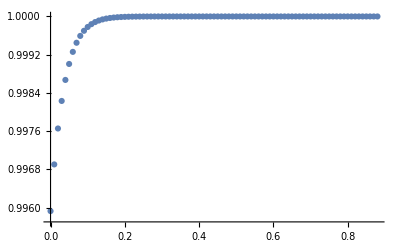
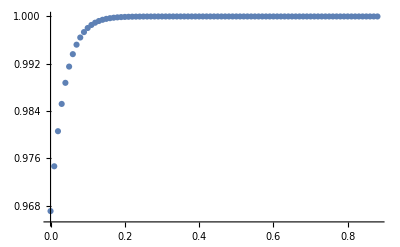
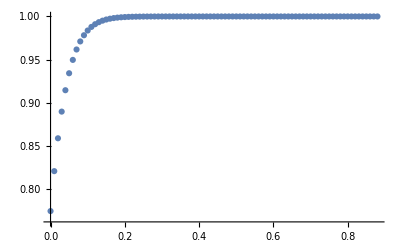
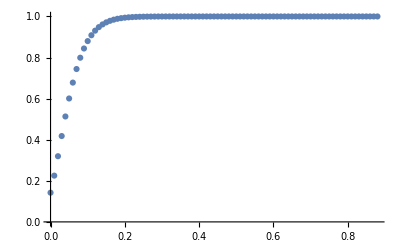
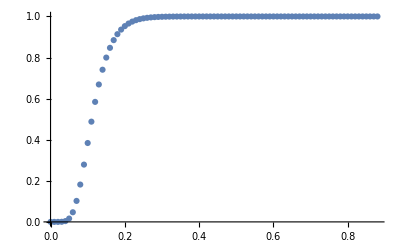

```mathematica
(*For a chosen value of σthreshold, we optimise ν for each value of n*)
hashingbound10 = Table[{ν , Max[0 , hashingbound[states10[ν]]]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingbound25 = Table[{ν , Max[0 , hashingbound[states25[ν]]]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingbound50 = Table[{ν , Max[0 , hashingbound[states50[ν]]]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingbound75 = Table[{ν , Max[0 , hashingbound[states75[ν]]]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingbound100 = Table[{ν , Max[0 , hashingbound[states100[ν]]]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
{ListPlot[hashingbound10 , PlotRange->All] , ListPlot[hashingbound25 , PlotRange->All] , ListPlot[hashingbound50 , PlotRange->All] , ListPlot[hashingbound75 , PlotRange->All] , ListPlot[hashingbound100 , PlotRange->All]}
```

General::munfl: 0.000822468^100 is too small to represent as a normalized machine number; precision may be lost.

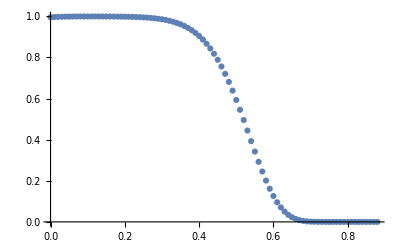
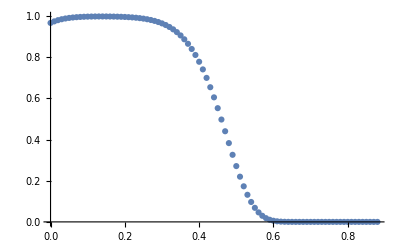
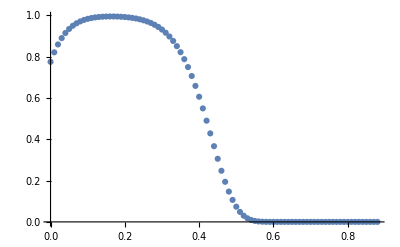
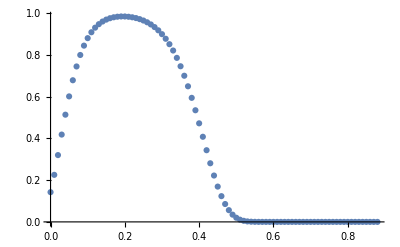
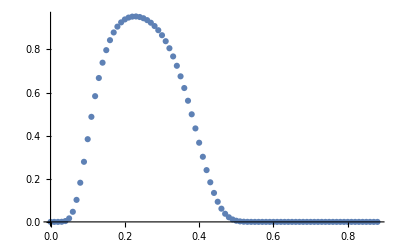

```mathematica
(*Hashing rate of chains of increasing length*)
hashingrate10= Table[{ν , ((Pc[σ , ν] + Pf[σ , ν])^2)^10 * hashingbound[states10[ν]]} , {ν , 0 , 0.5*Sqrt[π] , 0.01} ];
hashingrate25= Table[{ν , ((Pc[σ , ν] + Pf[σ , ν])^2)^25 * hashingbound[states25[ν]]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate50= Table[{ν , ((Pc[σ , ν] + Pf[σ , ν])^2)^50 * hashingbound[states50[ν]]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate75= Table[{ν , ((Pc[σ , ν] + Pf[σ , ν])^2)^75 * hashingbound[states75[ν]]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate100= Table[{ν , ((Pc[σ , ν] + Pf[σ , ν])^2)^100 * hashingbound[states100[ν]]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
{ListPlot[hashingrate10 , PlotRange->All] , ListPlot[hashingrate25 , PlotRange->All] , ListPlot[hashingrate50 , PlotRange->All] , ListPlot[hashingrate75 , PlotRange->All] , ListPlot[hashingrate100 , PlotRange->All]}
```

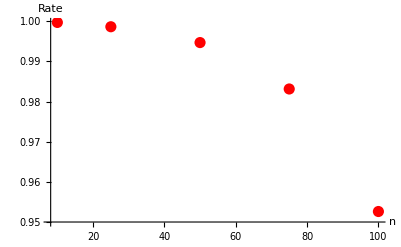

```mathematica
tab10 = Table[hashingrate10[[i , 2]] , {i , 1 , Length[hashingrate10]}];
tab25 = Table[hashingrate25[[i , 2]] , {i , 1 , Length[hashingrate25]}];
tab50 = Table[hashingrate50[[i , 2]] , {i , 1 , Length[hashingrate50]}];
tab75 = Table[hashingrate75[[i , 2]] , {i , 1 , Length[hashingrate75]}];
tab100 = Table[hashingrate100[[i , 2]] , {i , 1 , Length[hashingrate100]}];
rateplotvalues = {{10 , Max[tab10]} , {25 , Max[tab25]} , {50 , Max[tab50]} , {75 , Max[tab75]} , {100 , Max[tab100]}};
ListPlot[rateplotvalues , PlotRange->All , AxesStyle->Thick , AxesLabel->{"n" , "Rate"} , LabelStyle->Directive[Bold,18] , PlotStyle->{Red , PointSize->0.02}]
```

```mathematica
(*Single Rail state from Prajit's code - this state is not normalised so we take its trace and form the legitimate quantum state*)
SingleRailState[η_,γ_,Pd_,Vis_]:=2*{{(1-Pd) Pd γ^2,0,0,0},{0,(1-Pd) Pd (1-γ) γ (1-√η)+1/2 (1-Pd)^2 (1-γ) γ √η,1/2 (1-Pd)^2 (1-γ) γ √η*Vis,0},{0,1/2 (1-Pd)^2 (1-γ) γ √η*Vis,(1-Pd) Pd (1-γ) γ (1-√η)+1/2 (1-Pd)^2 (1-γ) γ √η,0},{0,0,0,(1-Pd) Pd (1-γ)^2 (1-√η)^2+(1-Pd)^2 (1-γ)^2 (1-√η) √η}}
(*Probability of Success*) 
PrSuccSingle[η_,γ_,Pd_,Vis_]:=Tr[SingleRailState[η,γ,Pd,Vis]]
(*SR quantum state*)
QStateSingle[η_,γ_,Pd_,Vis_]:=SingleRailState[η,γ,Pd,Vis]/Tr[SingleRailState[η,γ,Pd,Vis]]

(*Dual Rail state from Prajit's code - this state is not normalised so we take its trace and form the legitimate quantum state*)
DualRailState[η_,Pd_,Vis_]:=4*{{1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η,0,0,0},{0,1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η+1/16 (1-Pd)^4 η,1/16 (1-Pd)^4 η*Vis^2,0},{0,1/16 (1-Pd)^4 η*Vis^2,1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η+1/16 (1-Pd)^4 η,0},{0,0,0,1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η}}
(*Probability of Success*)
PrSuccDual[η_,Pd_,Vis_]:=Tr[DualRailState[η,Pd,Vis]]
(*SR quantum state*)
QStateDual[η_,Pd_,Vis_]:=DualRailState[η,Pd,Vis]/Tr[DualRailState[η,Pd,Vis]]

(*Defining the SR/DR states*)

(*Set η = 0.9 , γ = 0.5 , Pd = 0 , Vis = 1*)
(*Set η = 0.9 , Pd = 0 , Vis = 1*)

SR = QStateSingle[0.9 , 0.99 , 0 , 1];
DR = QStateDual[0.9 , 0 , 1];
```

```mathematica
(*Building up chains of SR/DR memories*)

(*SR*)
SR10tab = rNtimes[SR//Eigenvalues , 10];
SR25tab = rNtimes[SR//Eigenvalues , 25];
SR50tab = rNtimes[SR//Eigenvalues , 50];
SR75tab = rNtimes[SR//Eigenvalues , 75];
SR100tab = rNtimes[SR//Eigenvalues , 100];

(*building the state of my chains*)
SRstates10= SR10tab[[1]] Φplus + SR10tab[[2]] Φminus + SR10tab[[3]] Ψplus + SR10tab[[4]] Ψminus;
SRstates25= SR25tab[[1]] Φplus + SR25tab[[2]] Φminus + SR25tab[[3]] Ψplus + SR25tab[[4]] Ψminus;
SRstates50= SR50tab[[1]] Φplus + SR50tab[[2]] Φminus + SR50tab[[3]] Ψplus + SR50tab[[4]] Ψminus;
SRstates75= SR75tab[[1]] Φplus + SR75tab[[2]] Φminus + SR75tab[[3]] Ψplus + SR75tab[[4]] Ψminus;
SRstates100= SR100tab[[1]] Φplus + SR100tab[[2]] Φminus + SR100tab[[3]] Ψplus + SR100tab[[4]] Ψminus;

(*Finding the hashing rate by multiplying the probability of success by the hashing bound*)
SRhashingrate10 = Maximize[{PsuccSR[0.9 , γ]^10 * hashingbound[SRstates10] , 0<=γ<=1} , {γ}]
SRhashingrate25 = Maximize[{PsuccSR[0.9 , γ]^25 * hashingbound[SRstates25] , 0<=γ<=1} , {γ}]
SRhashingrate50 = Maximize[{PsuccSR[0.9 , γ]^50 * hashingbound[SRstates50] , 0<=γ<=1} , {γ}]
SRhashingrate75 = Maximize[{PsuccSR[0.9 , γ]^75 * hashingbound[SRstates75] , 0<=γ<=1} , {γ}]
SRhashingrate100 = Maximize[{PsuccSR[0.9 , γ]^100 * hashingbound[SRstates100] , 0<=γ<=1} , {γ}]
```

{0.00161209,{γ→0.444445}}

{1.03941×10^-7,{γ→0.430632}}

{1.096×10^-14,{γ→0.430632}}

{1.16103×10^-21,{γ→0.430632}}

{1.23372×10^-28,{γ→0.430632}}

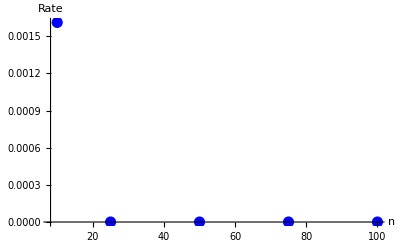

```mathematica
SRrateplotvalues = {{10 , SRhashingrate10[[1]]} , {25 , SRhashingrate25[[1]]} , {50 , SRhashingrate50[[1]]} , {75 , SRhashingrate75[[1]]} , {100 , SRhashingrate100[[1]]}};
ListPlot[SRrateplotvalues , PlotRange->All , AxesStyle->Thick , AxesLabel->{"n" , "Rate"} , LabelStyle->Directive[Bold,18] , PlotStyle->{Blue , PointSize->0.02}]
```

```mathematica
(*DR*)
DR10tab = rNtimes[DR//Eigenvalues , 10];

(*Weightings of Bell States do not change for DR case so we proceed with only 1000 chain*)

(*Building the state*)
DRstates10= DR10tab[[1]] Φplus + DR10tab[[2]] Φminus + DR10tab[[3]] Ψplus + DR10tab[[4]] Ψminus;

(*Finding the hashing bound*)
hashingbound[DRstates10]

(*Finding the hashing rate*)
DRhashingrate10 = Maximize[{PsuccDR[0.9 , γ]^10 * hashingbound[DRstates10] , 0<=γ<=1} , {γ}]
DRhashingrate25 = Maximize[{PsuccDR[0.9 , γ]^25 * hashingbound[DRstates10] , 0<=γ<=1} , {γ}]
DRhashingrate50 = Maximize[{PsuccDR[0.9 , γ]^50 * hashingbound[DRstates10] , 0<=γ<=1} , {γ}]
DRhashingrate75 = Maximize[{PsuccDR[0.9 , γ]^75 * hashingbound[DRstates10] , 0<=γ<=1} , {γ}]
DRhashingrate100 = Maximize[{PsuccDR[0.9 , γ]^100 * hashingbound[DRstates10] , 0<=γ<=1} , {γ}]
```

1.

{0.000340506,{γ→0.49995}}

{1.31611×10^-9,{γ→0.430632}}

{4.57747×10^-18,{γ→0.5}}

{9.79351×10^-27,{γ→0.5}}

{3.00037×10^-36,{γ→0.430632}}

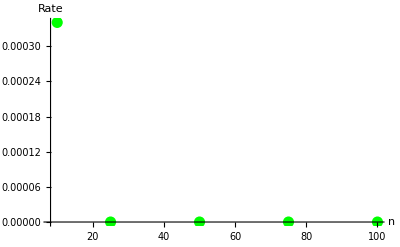

```mathematica
DRrateplotvalues = {{10 , DRhashingrate10[[1]]} , {25 , DRhashingrate25[[1]]} , {50 , DRhashingrate50[[1]]} , {75 , DRhashingrate75[[1]]} , {100 , DRhashingrate100[[1]]}};
ListPlot[DRrateplotvalues , PlotRange->All , AxesStyle->Thick , AxesLabel->{"n" , "Rate"} , LabelStyle->Directive[Bold,18] , PlotStyle->{Green , PointSize->0.02}]
```

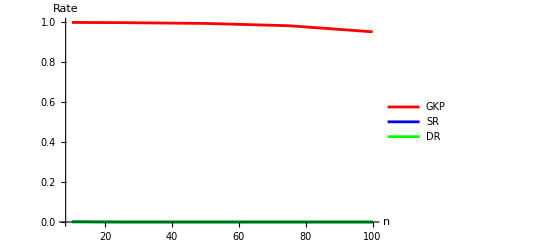

```mathematica
ListPlot[{rateplotvalues , SRrateplotvalues , DRrateplotvalues} , PlotRange->All , AxesStyle->Thick , AxesLabel->{"n" , "Rate"} , LabelStyle->Directive[Bold,18] , PlotStyle->{{Red , Thick} , {Blue , Thick} , {Green , Thick}} , Joined->True , PlotLegends->{"GKP" , "SR" , "DR"}]
```

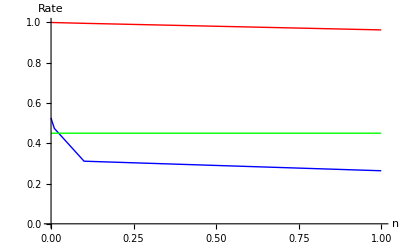
```mathematica
(*σthreshold = Sqrt[0.02]*)
-Graphics-
```

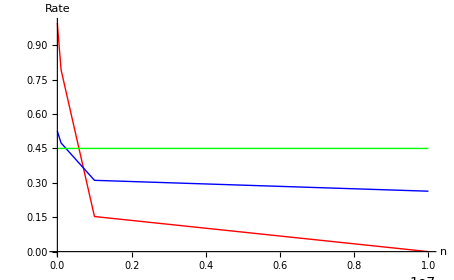
```mathematica
(*σthreshold = Sqrt[0.03]*)
-Graphics-
```

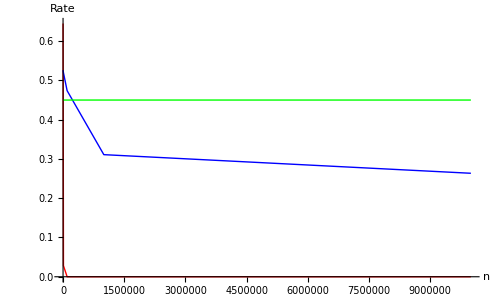
```mathematica
(*σthreshold = Sqrt[0.05]*)
-Graphics-
```